```mathematica
ClearAll["Global`*"]
```

# Input Mesh

Here we set input mesh for our project. Then cpp unit ../../user.cpp loads mesh data structure, (uniformly) refines it, and saves fine mesh + its ribs’ (edges’ middle points’) numeration—we will need this since ribs’ numeration is DOFs numeration for Crouzeix–Raviart shape funcs—to ../DrawInterpolant.

After that, we draw interpolants (component–wise for velocity, pressure, and common vector field + pressure distribution plots) and compute L_2–norms of errors. Check out ../DrawInterpolant/drawInterpolant.nb.

## Set Analytic Region Ω

One can set anything. Here we give a simple (yet geometrcally interesting) example.

```mathematica
Ω=RegionDifference[Rectangle[],Disk[{0,0},1/2]];
```

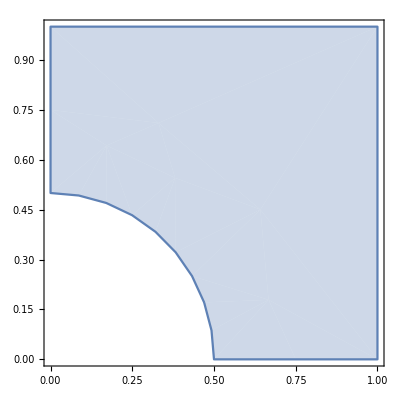

```mathematica
RegionPlot@Ω
```

## Create and Export Resulting Mesh 𝒯

```mathematica
NotebookEvaluate[NotebookDirectory[]<>"../../../Tools/Mathematica/triangulation.nb"]
```

```mathematica
𝒯=create𝒯fromRegion[Ω,.005];
```

```mathematica
highlight[𝒯,{"localNodesNumn","nodesNumn","trianglesNumn"}]
```

-Graphics-

### Export

```mathematica
(* set your home directory *)
SetDirectory@NotebookDirectory[];
export@𝒯
```